# NG^4 T_11.Архитектура свёрточных нейронных сетей

Шклярик Вера,
18-апр-2023

## Section. Извлечение признаков

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Subsection.Subsubsection. Загрузка набора растров ИмяНабора↦{Цифры,Растры}

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}]/255.;
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

#### Subsection.Subsubsection. Загрузка тренировочных шаблонов TrainLabel→TrainImage

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,28,28}}

#### Subsection.Subsubsection. Загрузка проверочных шаблонов TestLabel→TestImage

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,28,28}}

#### Subsection.Subsubsection. Загруженные наборы шаблонов

```mathematica
DynamicModule[{m=3},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[1-Train⟦2,n⟧,ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False,ControlPlacement->Top],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[1-Test⟦2,n⟧,ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False,ControlPlacement->Top]}},Frame->All,FrameStyle->Gray]]
```

Part::partd: Part specification Train⟦1,37267⟧ is longer than depth of object.

Part::partd: Part specification Train⟦2,37267⟧ is longer than depth of object.

Image::imgarray: The specified argument 1-Train⟦2,37267⟧ should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification Test⟦1,4655⟧ is longer than depth of object.

Part::partd: Part specification Test⟦2,4655⟧ is longer than depth of object.

Image::imgarray: The specified argument 1-Test⟦2,4655⟧ should be an array of rank 2 or 3 with machine-sized numbers.

### Subsection.Subsubsection. Извлечение признаков

```mathematica
Train[[1,3]]
```

4

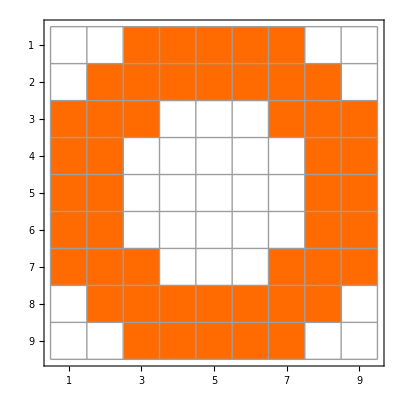

```mathematica
MatrixPlot[(Mask = DiskMatrix[4,9]-DiskMatrix[2,9]),Mesh->True]
```

```mathematica
Map[If[#<1,#-1,#]&,(DiskMatrix[4,9]-DiskMatrix[2,9]),{2}]
```

{{-1,-1,1,1,1,1,1,-1,-1},{-1,1,1,1,1,1,1,1,-1},{1,1,1,-1,-1,-1,1,1,1},{1,1,-1,-1,-1,-1,-1,1,1},{1,1,-1,-1,-1,-1,-1,1,1},{1,1,-1,-1,-1,-1,-1,1,1},{1,1,1,-1,-1,-1,1,1,1},{-1,1,1,1,1,1,1,1,-1},{-1,-1,1,1,1,1,1,-1,-1}}

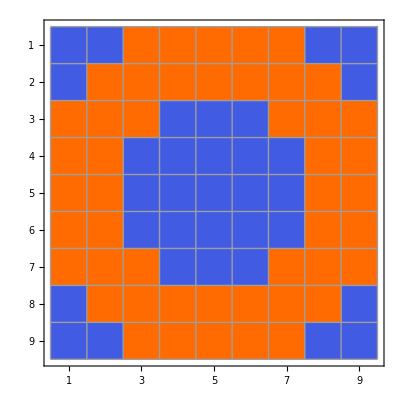

```mathematica
MatrixPlot[(Mask2 = Map[If[#<1,#-1,#]&,(DiskMatrix[4,9]-DiskMatrix[2,9]),{2}]),Mesh->True]
```

```mathematica
pos6 = Flatten@RandomSample[Position[Train[[1]],6],4]
pos8 = Flatten@RandomSample[Position[Train[[1]],8],4]
pos9 = Flatten@RandomSample[Position[Train[[1]],9],4]
```

{10136,23668,39737,51388}

{53849,33338,34947,57516}

{35594,16452,9877,31444}

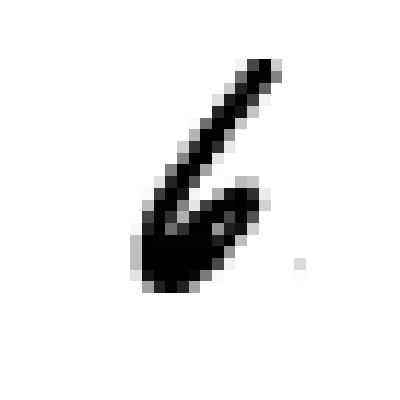
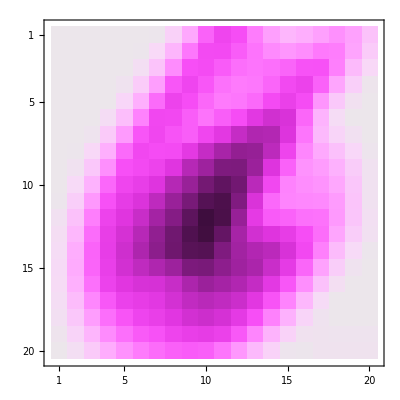
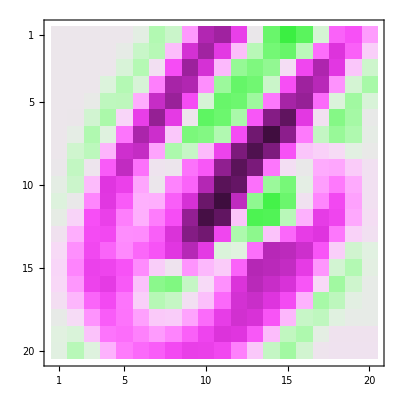
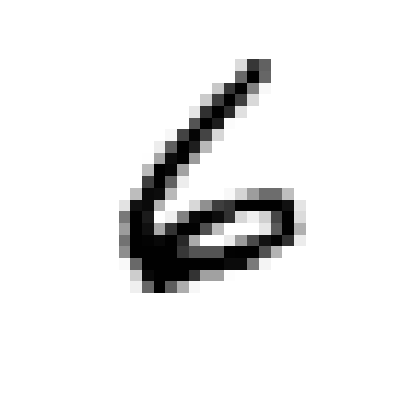
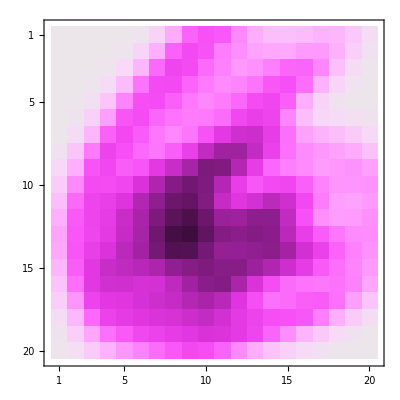
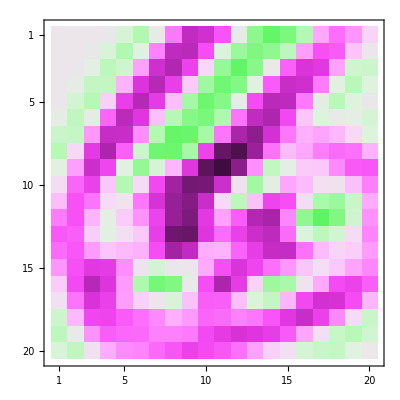
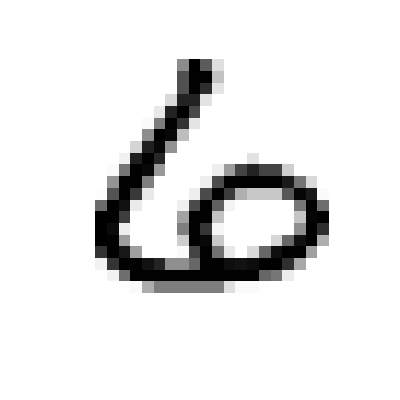
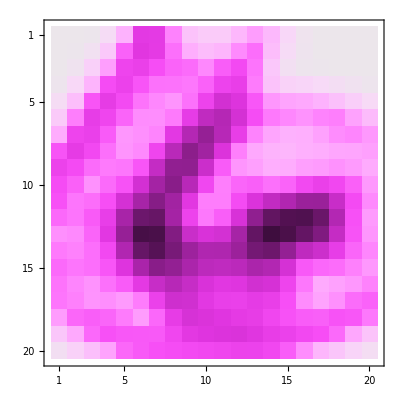
{-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-}

```mathematica
ArrayPlot@#->MatrixPlot[ListConvolve[Mask,#],ColorFunction->"GreenPinkTones"]->MatrixPlot[ListConvolve[Mask2,#],ColorFunction->"GreenPinkTones"]&/@Train[[2,pos6]]
```

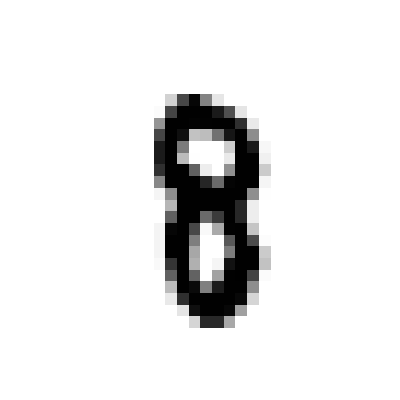
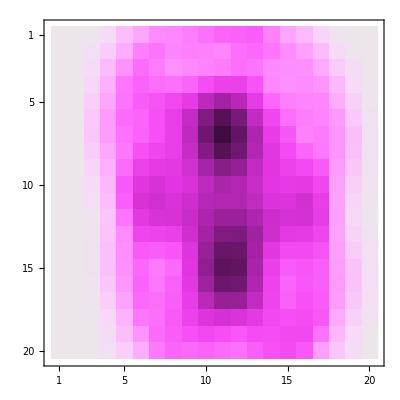
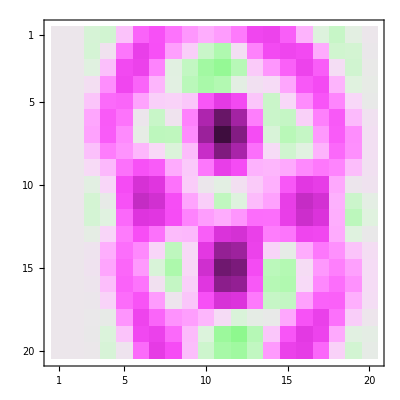
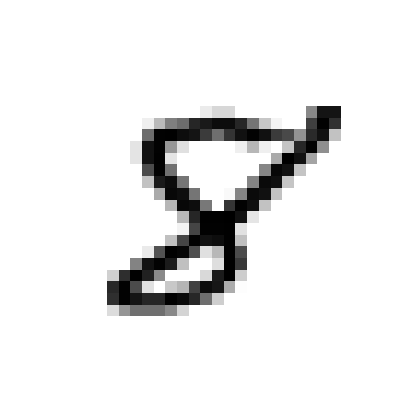
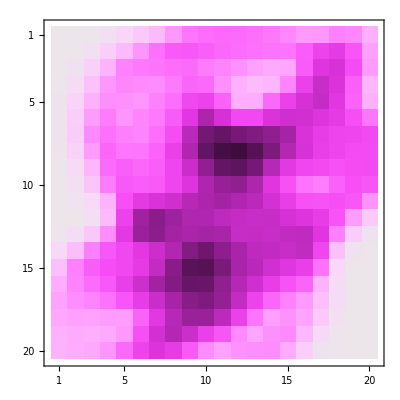
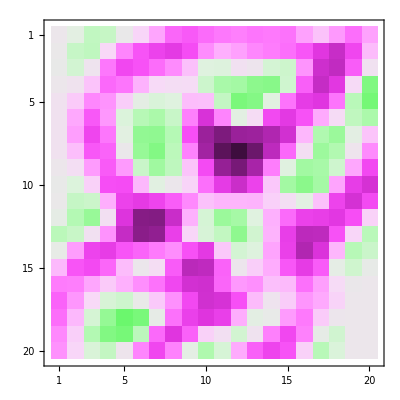
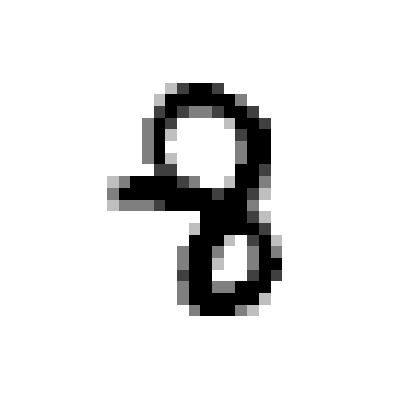
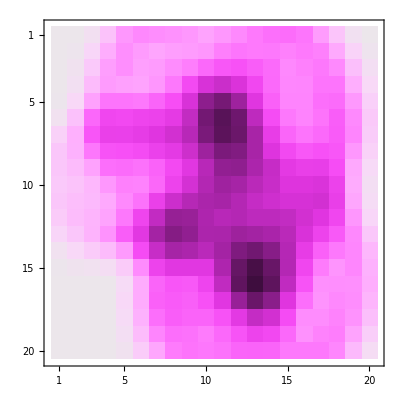
{-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-}

```mathematica
ArrayPlot@#->MatrixPlot[ListConvolve[Mask,#],ColorFunction->"GreenPinkTones"]->MatrixPlot[ListConvolve[Mask2,#],ColorFunction->"GreenPinkTones"]&/@Train[[2,pos8]]
```

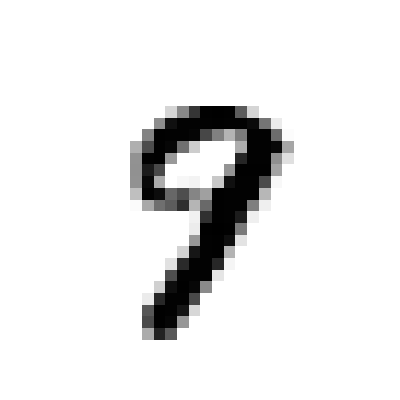
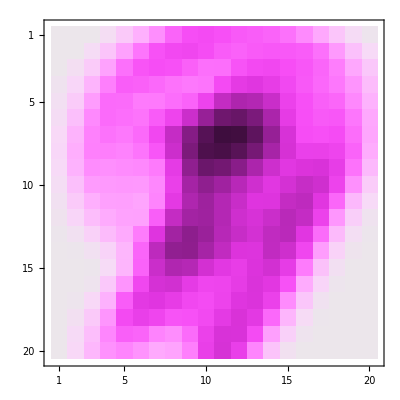
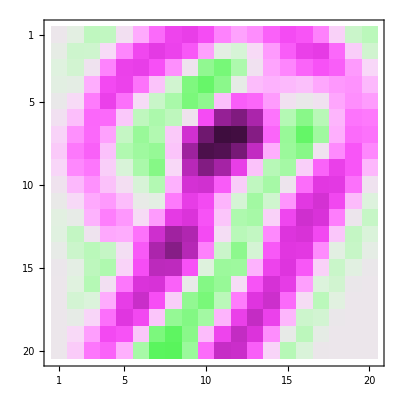
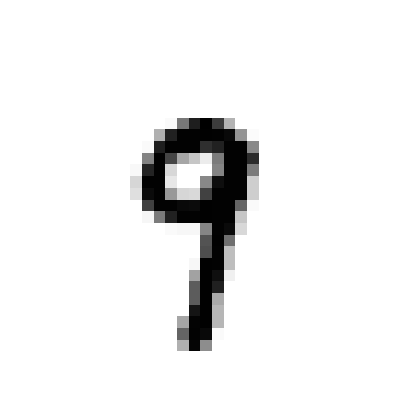
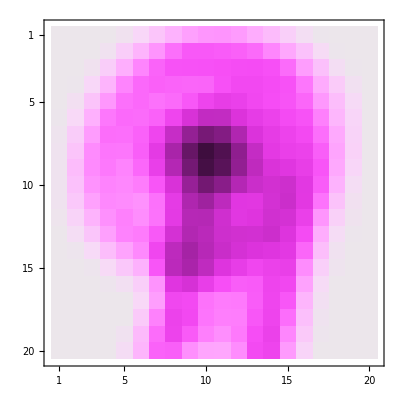
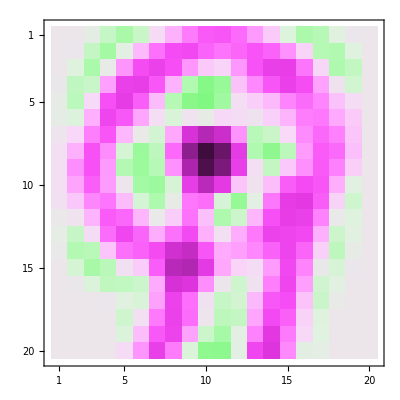
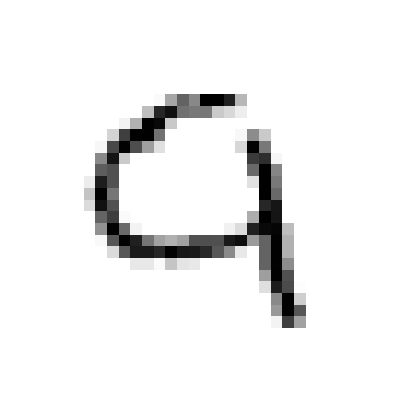
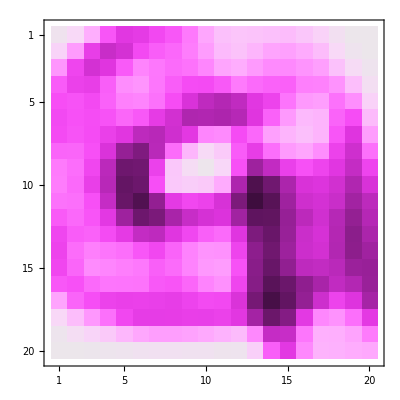
{-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-,-Graphics-→-Graphics-→-Graphics-}

```mathematica
ArrayPlot@#->MatrixPlot[ListConvolve[Mask,#],ColorFunction->"GreenPinkTones"]->MatrixPlot[ListConvolve[Mask2,#],ColorFunction->"GreenPinkTones"]&/@Train[[2,pos9]]
```

## Section. Свёрточный слой

### Section.Subsection. Подслой свёртки

```mathematica
kmWeight1 = {First@#,ArrayReshape[Rest@#,{5,5}]}&/@RandomReal[{-1,1},{6,26}];
Map[Dimensions,%,{2}]
```

{{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}},{{},{5,5}}}

```mathematica
ClearAll[kmConvolutionLayer1];
kmConvolutionLayer1 = Function[X,#1+ListConvolve[#2,X]&@@@kmWeight1]
```

Function[X,(#1+ListConvolve[#2,X]&)@@@kmWeight1]

```mathematica
RandomChoice@Train[[2]];
ArrayPlot[%,ImageSize->100]->Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,kmConvolutionLayer1@%]
```

-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Section.Subsection. Подслой активации

```mathematica
$ = RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->100]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$1 = kmConvolutionLayer1@$]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$2 = Ramp@$1]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Section.Subsection. Подслой подвыборки

```mathematica
$2//Dimensions
```

{6,24,24}

```mathematica
($3 =Partition[#,{2,2}]&/@$2)//Dimensions
```

{6,12,12,2,2}

```mathematica
Map[Max,$3,{3}]//Dimensions
```

{6,12,12}

```mathematica
ClearAll[kmPoolingLayer];
kmPoolingLayer = Function[X,Map[Map[Max,Partition[#,{2,2}],{2}]&,X]];
```

```mathematica
ArrayPlot[$,ImageSize->100]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$1 = kmConvolutionLayer1@$]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$2 = Ramp@$1]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$3 = kmPoolingLayer@$2]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Section. Многоканальные изображения

```mathematica
kmWeight2 = {First@#,ArrayReshape[Rest@#,{6,6,6}]}&/@RandomReal[{-1,1},{10,217}];
Map[Dimensions,%,{2}]
```

{{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}},{{},{6,6,6}}}

```mathematica
Count[kmWeight2,_Real,∞]
```

2170

### Section.Subsection. Подслой свёртки

```mathematica
ClearAll[kmConvolutionLayer2];
kmConvolutionLayer2 = Function[X,#1+ListConvolve[#2,X][[1,;;;;2,;;;;2]]&@@@kmWeight2]
```

Function[X,(#1+ListConvolve[#2,X]⟦1,1;;All;;2,1;;All;;2⟧&)@@@kmWeight2]

```mathematica
kmConvolutionLayer2@$3;
%//Dimensions
ArrayReshape[%%,{10,4,4}]//Dimensions
```

{10,4,4}

{10,4,4}

```mathematica
$ = RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->100]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$1 = $//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->60]&,$2 = $1//kmConvolutionLayer2]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image3D[ArrayReshape[#,{6,6,6}],ColorFunction->"GreenPinkTones"]&/@kmWeight2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Section.Subsection. Подслои активации и подвыборки

```mathematica
ArrayPlot[$,ImageSize->100]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$1 = $//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->60]&,$2 = $1//kmConvolutionLayer2]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->60]&,$3 = $2//Ramp]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->60]&,$4= $3//kmPoolingLayer]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Section. Полносвязный слой

```mathematica
kmWeight3 = {First@#,Rest@#}&/@RandomReal[{-1,1},{50,41}];
Map[Dimensions,%]
Count[kmWeight3,_Real,∞]
```

{{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}}

2050

```mathematica
$4//Dimensions
Flatten@$4;
#1+#2.%&@@@kmWeight3
```

{10,2,2}

{-18.3867,13.0823,-21.2735,108.258,139.757,38.8822,-50.4612,60.3629,-2.39645,122.353,-4.99624,-173.742,-123.938,96.6485,-108.033,-107.315,-18.3931,98.087,-8.20305,38.0056,-48.0529,14.5499,-34.8805,152.553,3.439,128.867,70.4367,8.79632,85.2114,-29.7606,26.3449,-18.0986,-57.0831,104.382,119.136,72.7399,-33.5326,8.82256,4.87233,112.115,-75.9002,-23.7256,-103.574,65.9143,-19.5723,-9.62775,46.51,6.22186,-78.0097,14.7459}

```mathematica
ClearAll[kmFullyConnectedLayer3,LReLU];
LReLU = If[#<0,0.01 #,#]&
kmFullyConnectedLayer3 =Function[X,Block[{x = Flatten@X},#1+#2.x&@@@kmWeight3]]
```

If[#1<0,0.01 #1,#1]&

Function[X,Block[{x=Flatten[X]},(#1+#2.x&)@@@kmWeight3]]

```mathematica
$4 //kmFullyConnectedLayer3//Dimensions
```

{50}

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

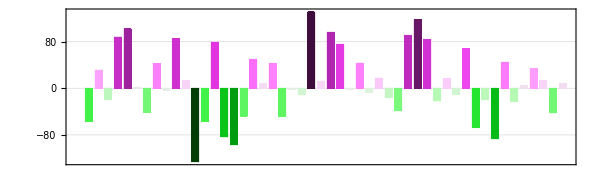

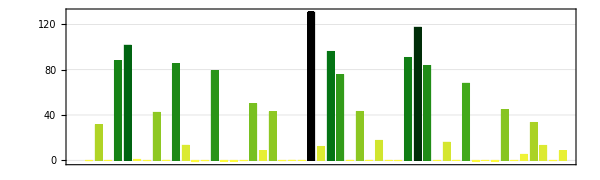

```mathematica
$ = RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->100]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->100]&,$1 = $//kmConvolutionLayer1//Ramp//kmPoolingLayer]
Map[MatrixPlot[#,ColorFunction->"GreenPinkTones", ImageSize->60]&,$2 = $1//kmConvolutionLayer2//Ramp//kmPoolingLayer]
BarChart[$3 = kmFullyConnectedLayer3@$2,ColorFunction->"GreenPinkTones",AspectRatio->.3,ImageSize->600,Frame->True,GridLines->Automatic]
BarChart[$4 =LReLU/@$3,ColorFunction->ColorData[{"AvocadoColors","Reverse"}],AspectRatio->.3,ImageSize->600,Frame->True,GridLines->Automatic]
```

## Section. Выходной слой с функцией активации SoftMax

```mathematica
SoftMax = SoftmaxLayer[]
```

SoftmaxLayer[<>]

```mathematica
%@$4
```

{0.,5.04467×10^-44,0.,2.27873×10^-19,2.18566×10^-13,0.,0.,3.47405×10^-39,0.,1.19697×10^-20,0.,0.,0.,2.69192×10^-23,0.,0.,0.,5.63733×10^-36,0.,4.56732×10^-39,0.,0.,0.,0.999998,0.,7.39366×10^-16,8.83441×10^-25,0.,7.08707×10^-39,0.,0.,0.,0.,3.48879×10^-18,1.66727×10^-6,2.94295×10^-21,0.,0.,0.,5.2806×10^-28,0.,0.,0.,3.79065×10^-38,0.,0.,4.11982×10^-43,0.,0.,0.}

```mathematica
kmWeight4= {First@#,Rest@#}&/@RandomReal[{-1,1},{10,51}];
Map[Dimensions,%,{2}]
Count[kmWeight3,_Real,∞]
```

{{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}},{{},{50}}}

2050

```mathematica
ClearAll[kmFullyConnectedLayer4];
kmFullyConnectedLayer4=Function[X,Block[{x = Flatten@X},#1+#2.x&@@@kmWeight4]]
```

Function[X,Block[{x=Flatten[X]},(#1+#2.x&)@@@kmWeight4]]

```mathematica
$4 //kmFullyConnectedLayer4//Dimensions
```

{10}

## Section. Свёрточная нейронная сеть

```mathematica
ClearAll[kmCNN];
kmCNN ["Init",maxW_:0.1]:=Block[{},kmWeight1 = {First@#,ArrayReshape[Rest@#,{5,5}]}&/@RandomReal[{-maxW,maxW},{6,26}]; kmWeight2 = {First@#,ArrayReshape[Rest@#,{6,6,6}]}&/@RandomReal[{-maxW,maxW},{10,217}];kmWeight3 = {First@#,Rest@#}&/@RandomReal[{-maxW,maxW},{50,41}];kmWeight4= {First@#,Rest@#}&/@RandomReal[{-maxW,maxW},{10,51}];]
kmCNN[X_]:= RightComposition[kmConvolutionLayer1,Ramp,kmPoolingLayer,kmConvolutionLayer2,Ramp,kmPoolingLayer,kmFullyConnectedLayer3,Map[LReLU],kmFullyConnectedLayer4,SoftMax]@X;
```

```mathematica
kmCNN["Init"]
$ = RandomChoice@Train[[2]];
ArrayPlot[$,ImageSize->100]
kmCNN@$
```

-Graphics-

{0.0998904,0.103689,0.0989341,0.103746,0.108944,0.0918848,0.0968254,0.0990754,0.100461,0.0965505}